# Transfer function of the 3320 VCF

See AS3320 datasheet.

Each filter stage consists of a variable gain current amplifier ΔA followed by a high input impedance buffer. CEM3320 datasheet says:

I_out = (I_ref - I_in) A_io e^(-Vc/Vt) where :

Vt=kT/q 
Vc=voltage applied to pin 12 (response: 60mV/decade or 18mV/octave ; an increasing value lowers the cutoff freq)
A_io = current amplifier gain (0.9 at Vc=0)
Iref = (0.46 * V_cc - 0.65)/100k = 62.5uA

Note that ΔA inputs (pins 1, 2, 17 and 18) are grounded through a forward biased diode => they all have a potential of 650mV.

DC regime : 
	I_ref=I_inso that I_out=0 and CAP "Cf" not charged.
	V_odc= optimal DC output voltage of each buffer should be 0.46 * V_cc = 6.9V
	This yields R_f= 100k and increasing R_F thus increases V_odc above 6.9V

The pole freq of each filter stage is given by:

fp = A_io/(2π R_eq C_p)e^(-Vc/Vt) where R_eq= R_f // 1MΩ

## Low pass topology

### Transfer function of a single LP cell: .10(A = A_io e^(-Vc/Vt))

```mathematica
Solve[{Iout == -A Iin, Iin == 1/Rc+Vout/Rf+Igm,Vout == Iout/(C p)},Vout,{Iout,Iin}]
```

{{Vout→-(A (1+Igm Rc) Rf)/(Rc (A+C p Rf))}}

For all stages except stage 1, Igm = 0 and we have:

```mathematica
TLP[p_]=-(Rf/Rc)/(1+(Rf C)/A p);
```

```mathematica
AN={Rf->100000, Rc->91000, C->300 10^-12, A-> 0.9 ⅇ^(-Vc/0.025)};
```

Cutoff:

```mathematica
fcutoff[Vc_]=(0.9 ⅇ^(-Vc/0.025))/(2π 100000 300 10^-12)
```

4774.65 ⅇ^(-40. Vc)

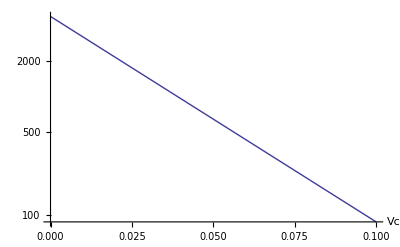

```mathematica
LogPlot[fcutoff[Vc],{Vc,0,.1},PlotRange->All,AxesLabel->Automatic]
```

### 4 stage transfer function with resonance control "Gm":

(resonance is explained in last page of datasheet)

```mathematica
Solve[Igm==-Gm (A (1+Igm Rc) Rf)/(Rc (A+C p Rf))TLP[p]TLP[p]TLP[p],Igm]
```

{{Igm→(A^4 Gm Rf^4)/(Rc (A^4 Rc^3+4 A^3 C p Rc^3 Rf+6 A^2 C^2 p^2 Rc^3 Rf^2+4 A C^3 p^3 Rc^3 Rf^3-A^4 Gm Rf^4+C^4 p^4 Rc^3 Rf^4))}}

```mathematica
TLPclosedLoop[p_]=(A^4  Rf^4)/(Rc (A^4 Rc^3+4 A^3 C p Rc^3 Rf+6 A^2 C^2 p^2 Rc^3 Rf^2+4 A C^3 p^3 Rc^3 Rf^3-A^4 Gm Rf^4+C^4 p^4 Rc^3 Rf^4))
```

(A^4 Rf^4)/(Rc (A^4 Rc^3+4 A^3 C p Rc^3 Rf+6 A^2 C^2 p^2 Rc^3 Rf^2+4 A C^3 p^3 Rc^3 Rf^3-A^4 Gm Rf^4+C^4 p^4 Rc^3 Rf^4))

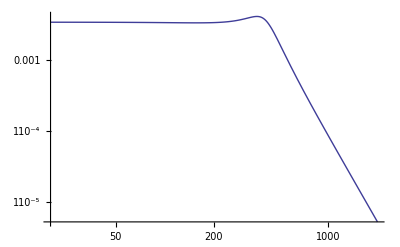

```mathematica
LogLogPlot[Abs[TLPclosedLoop[ⅈ 2 π f]]/.AN/.{Gm->3.6/54.6 0.05,Vc->0.1}//Evaluate,{f,20,2000},PlotRange->All]
```

## High pass topology

### Transfer function of a single HP cell: .10(A = A_io e^(-Vc/Vt))

```mathematica
Solve[{Iout == -A Iin, Iin == Vout/Rf,Vout==Iout/(C p)+Vin},Vout,{Iout,Iin}]
```

{{Vout→(C p Rf Vin)/(A+C p Rf)}}

```mathematica
THP[p_]=((Rf C)/A p)/(1+(Rf C)/A p)
```

(C p Rf)/(A (1+(C p Rf)/A))

## Bandpass topology

@Hugo : todo !